```mathematica
Needs["ErrorBarPlots`"]
video1coordinates = Import["/home/apawelek/Documents/video1coordinates.csv","CSV"];
video2coordinates = Import["/home/apawelek/Documents/video2coordinates.csv","CSV"];
video3coordinates = Import["/home/apawelek/Documents/video3coordinates.csv","CSV"];
video4coordinates = Import["/home/apawelek/Documents/video4coordinates.csv","CSV"];
video5coordinates = Import["/home/apawelek/Documents/video5coordinates.csv","CSV"];
video6coordinates = Import["/home/apawelek/Documents/video6coordinates.csv","CSV"];
video7coordinates = Import["/home/apawelek/Documents/video7coordinates.csv","CSV"];
video8coordinates = Import["/home/apawelek/Documents/video8coordinates.csv","CSV"];
video9coordinates = Import["/home/apawelek/Documents/video9coordinates.csv","CSV"];
video10coordinates = Import["/home/apawelek/Documents/video10coordinates.csv","CSV"];

(*
Features
[
which list (Frame number),
which set of points (which particle), 
x or y coordinate (in pixels)
]
*)
video1coordinates = Drop[video1coordinates,{301}]; (*Drop row 301*)
video1coordinates =Drop[video1coordinates,{},{11}]; (*Drop column 11*)
video2coordinates = Drop[video2coordinates,{},{1}];
video2coordinates = Drop[video2coordinates,{},{2}];
video2coordinates = Drop[video2coordinates,{},{10}];
video3coordinates = Drop[video3coordinates,{},{14}];
video4coordinates = Drop[video4coordinates,{},{2}];
video4coordinates = Drop[video4coordinates,{},{9}];
video6coordinates = Drop[video6coordinates,{},{15}];
video7coordinates = Drop[video7coordinates,{},{1}];
video7coordinates = Drop[video7coordinates,{},{4}];

For[i=1,
i< 301,
i++,
For[j=1,
j<11,
j++,
video1coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video1coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<14,
j++,
video2coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video2coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<14,
j++,
video3coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video3coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<10,
j++,
video4coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video4coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<18,
j++,
video5coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video5coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<15,
j++,
video6coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video6coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<5,
j++,
video7coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video7coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<4,
j++,
video8coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video8coordinates[[i,j]],("{"|"}")],","]
]
]

For[i=1,
i< 301,
i++,
For[j=1,
j<5,
j++,
video9coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video9coordinates[[i,j]],("{"|"}")],","]
]
]

For[i=1,
i< 301,
i++,
For[j=1,
j<6,
j++,
video10coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video10coordinates[[i,j]],("{"|"}")],","]
]
]
```

```mathematica
v1displacements =Array[0,{300,10}];
v2displacements= Array[0,{300,13}];
v3displacements=Array[0,{300,13}];
v4displacements= Array[0,{300,9}];
v5displacements=Array[0,{300,17}];
v6displacements= Array[0,{300,14}];
v7displacements=Array[0,{300,4}];
v8displacements= Array[0,{300,3}];
v9displacements= Array[0,{300,4}];
v10displacements= Array[0,{300,5}];


For[i=1,
i<301,
i++,
For[j=1,
j<11,
j++,
v1displacements[[i,j]] = (video1coordinates[[i,j,1]]-video1coordinates[[1,j,1]])^2+(video1coordinates[[i,j,2]]-video1coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<14,
j++,
v2displacements[[i,j]] = (video2coordinates[[i,j,1]]-video2coordinates[[1,j,1]])^2+(video2coordinates[[i,j,2]]-video2coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<14,
j++,
v3displacements[[i,j]] = (video3coordinates[[i,j,1]]-video3coordinates[[1,j,1]])^2+(video3coordinates[[i,j,2]]-video3coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<10,
j++,
v4displacements[[i,j]] = (video4coordinates[[i,j,1]]-video4coordinates[[1,j,1]])^2+(video4coordinates[[i,j,2]]-video4coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<18,
j++,
v5displacements[[i,j]] = (video5coordinates[[i,j,1]]-video5coordinates[[1,j,1]])^2+(video5coordinates[[i,j,2]]-video5coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<15,
j++,
v6displacements[[i,j]] = (video6coordinates[[i,j,1]]-video6coordinates[[1,j,1]])^2+(video6coordinates[[i,j,2]]-video6coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<5,
j++,
v7displacements[[i,j]] = (video7coordinates[[i,j,1]]-video7coordinates[[1,j,1]])^2+(video7coordinates[[i,j,2]]-video7coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<4,
j++,
v8displacements[[i,j]] = (video8coordinates[[i,j,1]]-video8coordinates[[1,j,1]])^2+(video8coordinates[[i,j,2]]-video8coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<5,
j++,
v9displacements[[i,j]] = (video9coordinates[[i,j,1]]-video9coordinates[[1,j,1]])^2+(video9coordinates[[i,j,2]]-video9coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<6,
j++,
v10displacements[[i,j]] = (video10coordinates[[i,j,1]]-video10coordinates[[1,j,1]])^2+(video10coordinates[[i,j,2]]-video10coordinates[[1,j,2]])^2
]
]

(*300 frames, 92 particles*)
alldisplacements = Join[v1displacements,v2displacements,v3displacements,v4displacements,v5displacements,v6displacements,v7displacements,v8displacements,v9displacements,v10displacements,2];
```

```mathematica
(*Frame,R^2*)
averagedisplacements = 
Table[
(1/92)*Sum[alldisplacements[[i,j]],{j,1,92}],
{i,1,300}
];
adjusteddisplacement = Table[((.12*10^(-6)))^2*averagedisplacements[[i]],{i,1,300}];

testaverageddisplacements = Table[
(1/92)*Sum[alldisplacements[[i,j]],{j,1,92}],
{i,1,180}
];
testadjusted = Table[((.12*10^(-6)))^2*testaverageddisplacements[[i]],{i,1,180}];

timesteps = Table[i/30,{i,0,299}];
testtimesteps = Table[i/30,{i,0,179}];

datapoints = Flatten[{timesteps,adjusteddisplacement},{{2},{1}}];
testdata =  Flatten[{testtimesteps,testadjusted},{{2},{1}}];

(*adjusteddatapoints =Flatten[{timesteps,averagedisplacements},{{2},{1}}];*)
```

2.1187×10^-14

2.14923×10^-25

FittedModel[-4.15907×10^-14+1.46685×10^-12 x]

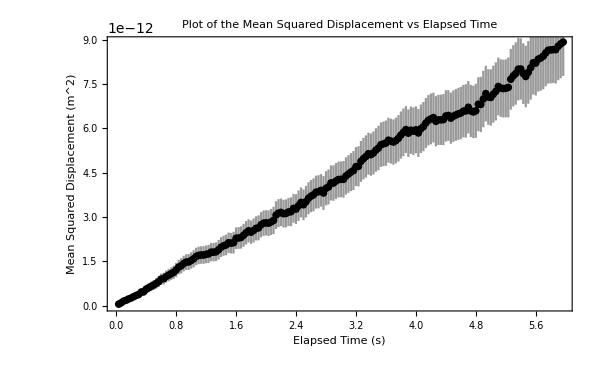

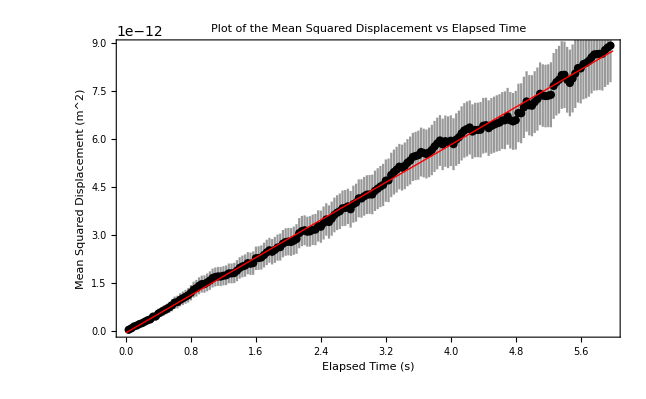

```mathematica
PositionError = 5.2;
r1uncertainty =Array[0,{300,10}];
r2uncertainty= Array[0,{300,13}];
r3uncertainty=Array[0,{300,13}];
r4uncertainty= Array[0,{300,9}];
r5uncertainty=Array[0,{300,17}];
r6uncertainty= Array[0,{300,14}];
r7uncertainty=Array[0,{300,4}];
r8uncertainty= Array[0,{300,3}];
r9uncertainty= Array[0,{300,4}];
r10uncertainty= Array[0,{300,5}];

For[i=1,
i<301,
i++,
For[j=1,
j<11,
j++,
r1uncertainty[[i,j]] = 2*PositionError*(Abs[(video1coordinates[[i,j,1]]-video1coordinates[[1,j,1]])]+Abs[(video1coordinates[[i,j,2]]-video1coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<14,
j++,
r2uncertainty[[i,j]] = 2*PositionError*(Abs[(video2coordinates[[i,j,1]]-video2coordinates[[1,j,1]])]+Abs[(video2coordinates[[i,j,2]]-video2coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<14,
j++,
r3uncertainty[[i,j]] = 2*PositionError*(Abs[(video3coordinates[[i,j,1]]-video3coordinates[[1,j,1]])]+Abs[(video3coordinates[[i,j,2]]-video3coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<10,
j++,
r4uncertainty[[i,j]] = 2*PositionError*(Abs[(video4coordinates[[i,j,1]]-video4coordinates[[1,j,1]])]+Abs[(video4coordinates[[i,j,2]]-video4coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<18,
j++,
r5uncertainty[[i,j]] = 2*PositionError*(Abs[(video5coordinates[[i,j,1]]-video5coordinates[[1,j,1]])]+Abs[(video5coordinates[[i,j,2]]-video5coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<15,
j++,
r6uncertainty[[i,j]] = 2*PositionError*(Abs[(video6coordinates[[i,j,1]]-video6coordinates[[1,j,1]])]+Abs[(video6coordinates[[i,j,2]]-video6coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<5,
j++,
r7uncertainty[[i,j]] = 2*PositionError*(Abs[(video7coordinates[[i,j,1]]-video7coordinates[[1,j,1]])]+Abs[(video7coordinates[[i,j,2]]-video7coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<4,
j++,
r8uncertainty[[i,j]] = 2*PositionError*(Abs[(video8coordinates[[i,j,1]]-video8coordinates[[1,j,1]])]+Abs[(video8coordinates[[i,j,2]]-video8coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<5,
j++,
r9uncertainty[[i,j]] = 2*PositionError*(Abs[(video9coordinates[[i,j,1]]-video9coordinates[[1,j,1]])]+Abs[(video9coordinates[[i,j,2]]-video9coordinates[[1,j,2]])])
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<6,
j++,
r10uncertainty[[i,j]] = 2*PositionError*(Abs[(video10coordinates[[i,j,1]]-video10coordinates[[1,j,1]])]+Abs[(video10coordinates[[i,j,2]]-video10coordinates[[1,j,2]])])
]
]

runcertainties = Join[r1uncertainty,r2uncertainty,r3uncertainty,r4uncertainty,r5uncertainty,r6uncertainty,r7uncertainty,r8uncertainty,r9uncertainty,r10uncertainty,2];

(*A list of error in each R^2 for each frame in pixels*)
averageuncertainties = 
Table[
(1/92)*Sqrt[Sum[(runcertainties[[i,j]])^2,{j,1,92}]],
{i,1,300}
];

(*Converted error, minus position 0*)
adjusteduncertainties = Table[
Sqrt[2*(.01/.12)^2+(averageuncertainties[[i]]/averagedisplacements[[i]])^2]*adjusteddisplacement[[i]],
{i,2,300}
];

delta = Sum[1/adjusteduncertainties[[i]]^2,{i,1,150}]*Sum[((i)/30)^2/adjusteduncertainties[[i]]^2,{i,1,150}]-(Sum[((i)/30)/adjusteduncertainties[[i]]^2,{i,1,150}])^2;

a = (1/delta)*(Sum[((i)/30)^2/adjusteduncertainties[[i]]^2,{i,1,150}]*Sum[adjusteddisplacement[[i]]/adjusteduncertainties[[i]]^2,{i,1,150}]-Sum[((i)/30)^2/adjusteduncertainties[[i]],{i,1,150}]*Sum[adjusteddisplacement[[i]]*((i)/30)/adjusteduncertainties[[i]]^2,{i,1,150}]);
b = (1/delta)*(Sum[1/adjusteduncertainties[[i]]^2,{i,1,150}]*Sum[adjusteddisplacement[[i]]*((i-1)/30)/adjusteduncertainties[[i]]^2,{i,1,150}]-Sum[((i-1)/30)^2/adjusteduncertainties[[i]],{i,1,150}]*Sum[adjusteddisplacement[[i]]/adjusteduncertainties[[i]]^2,{i,1,150}]);

sigmaa = Sqrt[(1/delta)*Sum[((i)/30)^2/adjusteduncertainties[[i]]^2,{i,1,150}]]
sigmab = Sqrt[(1/delta)*Sum[1/adjusteduncertainties[[i]]^2,{i,1,150}]];
sigmak = (1.21*10^(-23))Sqrt[(.01/1.02)^2+(sigmaa/(1.47*10^(-12)))^2+(1/293)^2]
kb = 1.21*10^(-23);

lm = LinearModelFit[testdata,x,x]

shitfit[x_] = a*x;
shitplot = Plot[shitfit[x],{x,0,5}];

fitplot = Plot[lm[x],{x,0,6}];
dataplot = ListPlot[testdata];


lm["ParameterTable"];
testdata[[2]];

errors = Array[0,{180,2}];
For[i=2,
i<181,
i++,
errors[[i,1]]= testdata[[i]];
errors[[i,2]] = ErrorBar[0,adjusteduncertainties[[i]]]
]

ErrorPlot = ErrorListPlot[errors,PlotStyle->Black,ErrorBarFunction->(ErrorBarPlots`Private`ebarfun[##]/.l_Line:>{Opacity@0.4,l}&),Frame->{{True,False},{True,False}}, FrameLabel->{{"Mean Squared Displacement (m^2)", None},{"Elapsed Time (s)",None}},PlotLabel->"Plot of the Mean Squared Displacement vs Elapsed Time"]
Show[ErrorPlot,Plot[lm[x],{x,0,6},PlotStyle->{Red,Thick}]]
```